Mathematical Techniques in Evolution and Ecology

# Some classic models in evolution and ecology

Based on chapter 3 in Otto and Day (2007)

Spring Quarter 2015
Simon Aeschbacher
saeschbacher@ucdavis.edu

## Outline

### Goals

To introduce/revisit some classic models in evolution and ecology

To derive dynamical equations, some of which will be analysed in later units

### Concepts

Exponential growth

Logistic growth

Linear and non-linear models

Symmetric models

Normalisation

Competition models

Not discussed, but in the book:

Consumer–resource models (e.g. predator–prey models)

SIR epidemiological models

## Exponential and logistic models of population growth

Common assumptions:

Constant environment

No interaction with other species (no competition, predation etc.)

Specific assumptions:

Exponential growth: constant amount of resources

Logistic growth: amount of resources decreases with increasing population size

### Exponential population growth

Assumes that the variable changes at a rate proportional to its current value.

All individuals reproduce (we can choose to model only the females)

Do not keep track of age → can account for nonoverlapping and overlapping generations

Variable: n(t) for the # of indiv. at time t

Parameters: b, per capita # of births (continuous time: birth rate); d, fraction of population dying (death rate)

Life-cycle and flow diagram:

#### Discrete-time version

Recursion equation (from the life-cycle diagram):

n (t+1)=(1-b) (1-d) n t

In this case, it does not matter whether births or deaths happen first. But recall the squirrel example, which included an immigration event!

Define the compound parameter R=(1-d)(1+b) as the number of surviving individuals per parent, or the reproductive factor. Hence

n (t+1)=R n (t)

Difference equation:

Δn=n (t+1)-n t=(R-1) n(t)

Define the discrete-time growth rate (per capita change in # of individuals) as r_d=R-1=b-d-b d.

#### Continuous-time version

Now, b and d denote the per capita rate of growth and death, respectively. Multiplied by a small amount of time Δt, they give the # of births and deaths per individual in this time interval.

Differential equation (from the flow diagram):

(ⅆ n)/ⅆt=b n(t)-d n(t)=r_c n(t),

where r_c=b-d is the per capita rate of change in the # of individuals.

### Logistic population growth

Many factors may slow the rate of growth, e.g. declining resource availability, increased predation risk, higher incidence of disease, etc. The logistic model describes this processes indirectly, and there are many ways of modeling the effect.

#### Discrete-time version

The standard logistic model in discrete time assumes that the number of surviving individuals per parent declines linearly with population size. That is, the reproductive factor is modelled as

R(n)=intercept+slope * n(t) =(1+r_d)+(-r_d/K)n(t),

where K is the carrying capacity.

The population grows, i.e. R(n)>1, if n(t)<K.

The population shrinks, i.e. R(n)<1, if n(t)>K.

No change occurs if n(t)=K.

```mathematica
logGrowthReproFactorPlot
```

Recursion equation:

n(t+1)=R(n) n(t)=[(1+r_d)-r_d/K n(t)]n(t)=n(t)+r_d n(t)(1-(n(t))/K).

Difference equation:

Δn=n(t+1)-n(t)=r_d n(t)(1-(n(t))/K).

#### Continuous-time version

We leave the derivation of the differential equation as homework (Problem 2).

#### Illustration: Discrete-time version of logistic growth model

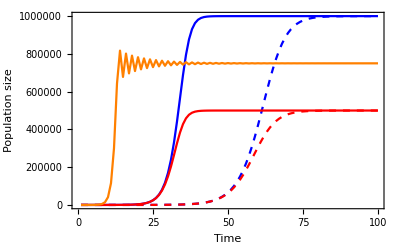

```mathematica
plotLogGrowth[(* K: *){10^6,10^6,5 10^5,5 10^5,7.5 10^5},(* r: *){0.5,0.25,0.5,0.25,1.9},(* tMax: *){100,100,100,100,100},(* Style: *){{Blue},{Blue,Dashed},{Red},{Red,Dashed},{Orange}}]
```

Notice the cyclic behaviour, eventually converging to K=750000, of the orange line. This occurs if r_d is above a critical value, such that n(t) can overshoot K and, hence, R(n) becomes negative. This behaviour is obseverd only in the discrete-time model.

## Linear and nonlinear models

Linear models: The change per unit time is a linear function of the variable(s)

Example: Exponential growth model, Δn=(R-1) n(t)=r_d n(t).

Nonlinear models: The change per unit time is a ‘more complicated’, non-linear function of the variable(s)

Example: Logistic growth model, Δn=r_d n(t)(1-(n(t))/K)=r_d n(t)-r_d(n(t))^2/K.

It is straightforward to obtain the general solution of linear models, i.e. there is an explicit solution predicting what the value of the variable will be at any future point in time (See unit 6 / chapter 6).

However, for non-linear models, this can be difficult or even impossible. In biology, most models are non-linear, as they often involve interactions.

Remark: Recursion, difference, and differential equations are implicit descriptions.

## Haploid and diploid models of natural selection

We will study two basic, but very important deterministic population-genetic models. Population-genetic models describe how the frequency of alleles changes over time. We consider one locus with two alleles called A and a, where one allele is favoured over the other by natural selection.
Sexual organisms go through a haploid and a diploid phase in their life cycle. Whether the haploid or diploid model of selection is appropriate depends on when selection acts:

### Haploid model of selection

Assume that the population is censused immediately after the generation of haploids (gametes)

Denote the # of A and a carriers at time t by n_A(t) and n_a(t), respectively

Assume that there is no mutation

Each type survives and reproduces according to the exponential growth model, with type-specific reproductive factors. The convention is to denote these by W: W_A=(1-d_A)(1+b_A) and W_a=(1-d_a)(1+b_a).

Recursion equations in terms of absolute numbers:

n_A(t+1)=W_A n_A(t)

n_a(t+1)=W_a n_a(t)

#### Symmetric models

In a symmetric model, the labels of the variables are arbitrary; interchanging the variable and parameter names does not alter the form of the equations. The haploid model of selection is a symmetric model.

### Haploid model continued

To express the dynamics in terms of allele frequencies, set p(t)=n_A(t)/[n_A(t)+n_a(t)] and q(t)=1-p(t)=n_a(t)/[n_A(t)+n_a(t)]. Note that p(t)+q(t)=1, so that the dynamics can be described in terms of only one variable. Substitution yields

p(t+1)=(n_A(t+1))/(n_A(t+1)+n_a(t+1))=(W_A n_A(t))/(W_A n_A(t)+W_a n_a(t)).

To express the right-hand side in terms of p(t), divide the numerator and denominator by n_A(t)+n_a(t) to obtain

p(t+1)=(W_A p(t))/(W_A p(t)+W_a(1-p(t))).

The reproductive factors W_A and W_a are called absolute fitnesses. Dividing the numerator and denominator by W_a, we can reduce the number of parameters:

p(t+1)=(V_A p(t))/(V_A p(t)+1-p(t)).

V_A=W_A/W_a is the relative fitness of allele A. We could also divide by W_A, instead.

The fact that the dynamics depends only on the relative fitnesses is important. Even if fitnesses depend on time (i.e. on the ecological context), the equation above holds, as long as the ecological context affects both alleles in the same way.

### Haploid model continued

Difference equation:

Δp=(W_A p(t))/(W_A p(t)+W_a(1-p(t)))-p(t)=p(t)(1-p(t))(W_A-W_a)/(W_A p(t)+W_a(1-p(t))).

Note that the denominator is equal to the mean (relative) fitness, W̄=W_A p(t)+W_a(1-p(t)).

Note also that Δp is proportional to the variance of the allele frequency, p(t)(1-p(t)).

It is useful to define the selection coefficient as s_d=(W_A-W_a)/W_a, i.e. the proportional difference in fitnesses. The difference equation becomes

Δp=p(t)(1-p(t))s_d/(1+s_d p(t)).

#### Let us derive the differential equation from the difference equation:

(ⅆp(t))/ⅆt=

What happens if one of the two alleles is absent?

At what frequency p(t) is the rate of change maximised?

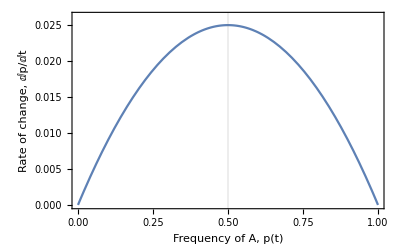

```mathematica
GraphicsColumn[{plotHaploSelChange,plotHaploSelMod}]
```

### Diploid model of selection

With two alleles, we must keep track of three genotypes, AA, Aa, and aa. We assume that Aa and aA are equivalent w.r.t. selection. Instead of repeating the steps undertaken for the haploid model, we take three shortcuts often used in deriving evolutionary models.

Census the population at the stage that is simplest to describe. In this case, this is the gamete stage, when there are only two types, A and a, with frequencies p(t) and q(t)=1-p(t). With random mating, genotype frequencies are easily computed according to the Hardy–Weinberg proportions.

Recognise that selection alters genotype frequencies proportionally to their fitness. This requires normalisation by the mean fitness,

W̄=p(t)^2 W_AA+2p(t)q(t)W_Aa+q(t)^2 W_aa.

With Mendelian segregation during meiosis, the percentage of gametes carrying A is 100% from AA parents, 50% from Aa parents, and 0% from aa parents.

Let us complement the following table applying these three steps:

```mathematica
diplSelTable
```

Gametes
uniting to
zygote | Freqency
before
selection | Frequency
weighted
by fitness | Frequency
after
selection | Gamete proportions
among offspring
     A             a
A Cell["×"] A |  |  |  | 
A Cell["×"] a |  |  |  | 
a Cell["×"] A |  |  |  | 
a Cell["×"] a |  |  |  |

Multiplying the frequency of the adults after selection by the proportion of gametes produced, and taking the appropriate sums, we obtain

p(t+1)=p(t)^2 W_AA/(W̄)+p(t)q(t)W_Aa/(W̄),

q(t+1)=p(t)q(t)W_Aa/(W̄)+(q(t))^2 W_aa/(W̄).

Convince yourself that p(t+1)+q(t+1)=1 holds.

#### Exercise

(a) Show that the mean fitness W̄ cen be written in terms of the composite or marginal fitnesses

W_(A^*)=p(t)W_AA+q(t)W_Aa,

and

W_(a^*)=p(t)W_Aa+q(t)W_aa.

(b) Show that the diploid recursion equations (17) and (18) can be written in a form equivalent to the haploid recursion equation with W_(A^*) and W_(a^*) taking the places of W_A and W_a, respectively.

## The Lotka–Volterra model of competition

The Lotka–Volterra model extends the logistic model by allowing multiple species to compete for resources, resulting in both intra- and interspecific competition.

Assume two species whose numbers are n_1(t) and n_2(t), and who have their specific intrinsic growth rate r_i and carrying capacity K_i.

The key is to assume that each individual of species i experiences competition as if its own species had a population size of n_i(t)+α_(i,j)n_j(t).
The parameter α_(i,j) is the competition coefficient, which converts the strength of competition caused by an individual of species j on an individual of species i into the equivalent amount of intraspecific competition in species i. Assuming a linear effect of competition, we have

R_i=(1+r_i)+(-r_i/K_i)(n_i(t)+α_(i,j)n_j(t)).

Plugging this into the recursion equation for the logistic model, we obtain

n_i(t+1)=n_i(t)+r_i n_i(t)(1-(n_i(t)+α_(i,j)n_j(t))/K_i)  for i,j ∈{1,2}.

The corresponding continuous-time differential equations are

(ⅆ n_i)/ⅆt=r_i n_i(t)(1-(n_i(t)+α_(i,j)n_j(t))/K_i)  for i,j ∈{1,2}.

Remark: We have interpreted the α_(i,j) as a competition coefficients, but in fact they can be used to model species interactions more generally. The signs of the coefficients reflect the type of relationship:

```mathematica
specRelTable
```

α_(1, 2) | α_(2, 1) | Relationship
- | - | Mutualistic (both profit)
- | 0 | Commensal (species 1 profits)
0 | - | Commensal (species 2 profits)
+ | - | Parasitic (species 1 is host)
- | + | Parasitic (species 2 is host)
+ | + | Competitive (both suffer)

## Problem assignment

We constructed the differential equation for the continuous-time version of the exponential growth model from the flow diagram. (a) Instead, derive the equation from the difference equation of the discrete-time version. Hint: introduce a small amount of time Δt and take the appropriate limit. (b) Comparing r_d and r_c, explain the difference between the discrete- and continuous-time versions.

Derive the differential equation for the logistic growth model in continuous time. Start by assuming that the per capita growth rate r(n) declines linearly with population size n(t). Assume that r(n) has a maximum equal to the intrinsic growth rate r_c when there are no competitors (i.e. r(0)=r_c), and that it reaches zero when the population is at the carrying capacity (i.e. r(K)=0). Substitute r(n) for r_c in the differential equation of the exponential growth model to obtain the result of interest.

As an alternative way of deriving the continuous-time version of the haploid selection model, start from the continous-time version of the exponential growth model. Specifically, let n_A and n_a be the number of individuals carrying alleles A and a, respectively, and let the growth rate depend on the allelic state, i.e. r_A=(b_A-d_A) for carriers of A, and r_a=(b_a-d_a) for carriers of a. From the exponential growth model, we have (ⅆ n_A)/ⅆt=r_A n_A(t) and (ⅆ n_a)/ⅆt=r_a n_a(t). But we want to know how the allele frequencies change! As these sum to 1, it is sufficient to follow only the frequency of allele A, p(t)=n_A(t)/[n_A(t)+n_a(t)] . Start by writing

(ⅆp(t))/ⅆt=ⅆ[(n_A(t))/(n_A(t)+n_a(t))]/ⅆt,

then use the quotient rule to evaluate the derivative, and use the equations for (ⅆ n_A)/ⅆt and (ⅆ n_a)/ⅆt to express ⅆp/ⅆt in terms of r_A, r_a, and p.

## Initialisation cells

```mathematica
logGrowthReproFactor[n_,rd_,K_]:=(1+rd)-rd/K n
```

```mathematica
logGrowthReproFactorPlot:=Manipulate[
Plot[logGrowthReproFactor[n,rd,K],{n,0,2K},
PlotRange->{{0,2K},{0,1.05(1+rd)}},
Frame->True,
FrameLabel->{{"Reproductive factor, R(n)",""},{"Population size, n(t)","K = "<>ToString[ Round[K]]<>"; r_d = "<>ToString[Round[rd,0.01]]}},
LabelStyle->Directive[FontFamily->"Helvetica", FontSize->14],
GridLines->{{K},{1}}],
{{rd,1},0,2},{{K,100},10,200}
]
```

```mathematica
Clear[n]
n[0,KK_,r_]:=n[0,KK,r]=1;
n[t_,KK_,r_]:=n[t,KK,r]=N[n[t-1,KK,r]+r n[t-1,KK,r](1-n[t-1,KK,r]/KK)]
```

```mathematica
plotDataListLogGrowth[KK_,r_,tMax_]:=Table[n[t,KK,r]//N,{t,1,tMax}]
```

```mathematica
plotLogGrowth[KList_,rList_,tMaxList_,styleList_]:=
ListLinePlot[MapThread[plotDataListLogGrowth[#1,#2,#3]&,{KList,rList,tMaxList}],
Frame->True,
FrameLabel->{"Time","Population size"},
LabelStyle->{FontFamily->"Helvetica",FontSize->14},
PlotStyle->styleList
]
```

```mathematica
plotHaploSelMod:=Manipulate[
Plot[
(1+(1-p0)/p0 ⅇ^(-s t))^-1,{t,0,120},PlotRange->{Full,{0,1.05}},
Frame->True,
FrameLabel->{"Time, t","Frequency of A, p(t)"},
LabelStyle->Directive[FontFamily->"Helvetica", FontSize->14]
],
{{p0,0.01},0.0001,1.0},{{s,0.1},0.,1.}]
```

```mathematica
plotHaploSelChange:=Plot[
p(1-p)s/.{s->0.1},{p,0,1},PlotRange->{Full,{0,1.05*1/4 s}/.{s->0.1}},
Frame->True,
FrameLabel->{{"Rate of change, ⅆp/ⅆt",""},{"Frequency of A, p(t)","s = 0.1"}},
LabelStyle->Directive[FontFamily->"Helvetica", FontSize->14],
GridLines->{{0.5},{}}
]
```

```mathematica
diplSelTableData:={
{Column[{"Gametes","uniting to", "zygote"}, Left], Column[{"Freqency","before","selection"},Left], Column[{"Frequency","weighted", "by fitness"},Left], Column[{"Frequency","after", "selection"},Left],Column[{"Gamete proportions","among offspring","     A             a"}]},

{Column[{"A Cell["×"] A"},Left],Column[{""},Left],Column[{""},Left],Column[{""},Left]},

{Column[{"A Cell["×"] a"},Left],Column[{""},Left],Column[{""},Left],Column[{""},Left]},

{Column[{"a Cell["×"] A"},Left],Column[{""},Left],Column[{""},Left],Column[{""},Left]},

{Column[{"a Cell["×"] a"},Left],Column[{""},Left],Column[{""},Left],Column[{""},Left]}
}
```

```mathematica
diplSelTable=Grid[diplSelTableData,Spacings->{1,1},ItemStyle->"Text",Alignment->Left,Frame->All,Background->{{None,None},{LightGray,None}}];
```

```mathematica
specRelTableData:={
{Column[{"α_(1, 2)"}, Center], Column[{"α_(2, 1)"},Center], Column[{"Relationship"},Center]},

{Column[{"-"}, Center], Column[{"-"},Center], Column[{"Mutualistic (both profit)"},Center]},

{Column[{"-"}, Center], Column[{"0"},Center], Column[{"Commensal (species 1 profits)"},Center]},

{Column[{"0"}, Center], Column[{"-"},Center], Column[{"Commensal (species 2 profits)"},Center]},

{Column[{"+"}, Center], Column[{"-"},Center], Column[{"Parasitic (species 1 is host)"},Center]},

{Column[{"-"}, Center], Column[{"+"},Center], Column[{"Parasitic (species 2 is host)"},Center]},

{Column[{"+"}, Center], Column[{"+"},Center], Column[{"Competitive (both suffer)"},Center]}
}
```

```mathematica
specRelTable=Grid[specRelTableData,Spacings->{1,1},ItemStyle->"Text",Alignment->Center,Frame->All,Background->{{None,None},{LightGray,None}}];
```